# Lab 1 | Modeling Old Faithful' s Eruptions

```mathematica
Modeling Data
```

Observations

Some observations about Old Faithful’s eruptions are listed below

•   On the average, eruptions reach heights of 106 to 184 feet and last 1.5 to 5.5 minutes.
•  The interval between eruptions can be as short as 30 minutes or as long as 2 hours.
•  The yearly average for the interval between eruptions has always been between 60 and 79   minutes.
•  The temperature of water at Old; Faithful’s vent is about 204°F.

Purpose

In this model, I will model the data on Old Faithful’s eruptions and the interval between the eruptions. I will compare my model with the model found using Mathematica and the model Yellowstone Park uses to predict Old Faithful eruptions to see if I can describe what it means to have a “best-fitting” model.

## Data

```mathematica
data = {{1.80,56},{1.82,58},{1.88,60},{1.90,62},{1.92,60},{1.93,56},{1.98,57},{2.03,60},{2.05,57},{2.13,60},{2.30,57},{2.35,57},{2.37,61},{2.82,73},{3.13,76},{3.27,77},{3.65,77},{3.70,82},{3.78,79},{3.83,85},{3.87,81},{3.88,80},{4.10,89},{4.27,90},{4.30,84},{4.30,89},{4.43,84},{4.43,89},{4.47,86},{4.47,80},{4.53,89},{4.55,86}, {4.60,88},{4.60,92},{4.63,91}};
```

```mathematica
colheading = {"Duration, x", "Interval, y"};
datatable = TableForm[data, TableHeadings->{None, colheading},TableAlignments->{Center, Center}];
```

```mathematica
datatable
```

Duration, x | Interval, y
1.8 | 56
1.82 | 58
1.88 | 60
1.9 | 62
1.92 | 60
1.93 | 56
1.98 | 57
2.03 | 60
2.05 | 57
2.13 | 60
2.3 | 57
2.35 | 57
2.37 | 61
2.82 | 73
3.13 | 76
3.27 | 77
3.65 | 77
3.7 | 82
3.78 | 79
3.83 | 85
3.87 | 81
3.88 | 80
4.1 | 89
4.27 | 90
4.3 | 84
4.3 | 89
4.43 | 84
4.43 | 89
4.47 | 86
4.47 | 80
4.53 | 89
4.55 | 86
4.6 | 88
4.6 | 92
4.63 | 91

```mathematica
dataplot = ListPlot[data,DataRange -> {1,5},AxesLabel->{HoldForm["Duration, x"],HoldForm["Interval,y"]}, PlotLabel->"Old Faithful Eruptions" ];
```

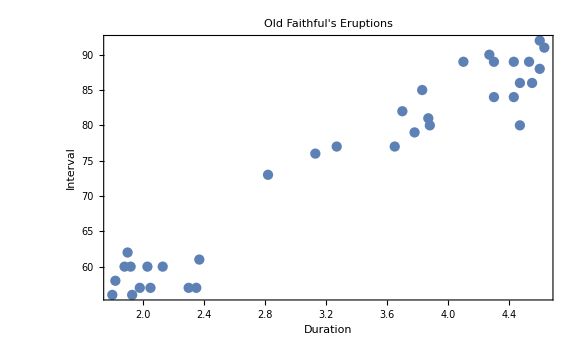

```mathematica
Show[dataplot,PlotLabel-> "Old Faithful's Eruptions",FrameLabel->{{HoldForm["Interval"],None},{HoldForm["Duration"],None}} ,LabelStyle->{"Times New Roman", 14, GrayLevel[0],Bold}, ImageSize->Large,Frame-> True]
```

1. Describe the Relationship.